# MAT: 150 -- Lab 1

## Date: 8/25/2017 Due: 8/28/2017

Adapted from notebook by Richard Neidinger, Davidson College

## Systems of Linear Equations

We store a system of linear equations as an augment matrix. Matrices in Mathematica can be entered row-wise using the { } notation.

```mathematica
aug={{1,2,-1,6},{2,4,-1,5},{-5,2,3,7}}
```

{{1,2,-1,6},{2,4,-1,5},{-5,2,3,7}}

We can compute the row reduced echelon form of this augment matrix using the command below:

```mathematica
RowReduce[aug]
```

{{1,0,0,-29/6},{0,1,0,23/12},{0,0,1,-7}}

From which we see that the unique solution vector is (-29/6,23/12,-7). The solution vector can be extracted as follows:

```mathematica
ans=RowReduce[aug];
ans[[All,4]]
```

{-29/6,23/12,-7}

### Elementary Row Operations

We will perform the necessary row operations to reduce aug to echelon form.

```mathematica
R=aug
R[[2]]=R[[2]]-2*R[[1]];R
R[[3]]=R[[3]]+5*R[[1]];R
R[[{2,3}]]=R[[{3,2}]];R
```

{{1,2,-1,6},{2,4,-1,5},{-5,2,3,7}}

{{1,2,-1,6},{0,0,1,-7},{-5,2,3,7}}

{{1,2,-1,6},{0,0,1,-7},{0,12,-2,37}}

{{1,2,-1,6},{0,12,-2,37},{0,0,1,-7}}

At this point, the system may be solved using back-substitution:

```mathematica
sol={0,0,0};
sol[[3]]=R[[3,4]]/R[[3,3]];
sol[[2]]=(R[[2,4]]-R[[2,3]]*sol[[3]])/R[[2,2]];
sol[[1]]=(R[[1,4]]-R[[1,3]]*sol[[3]]-R[[1,2]]*sol[[2]])/R[[1,1]];sol
```

{-29/6,23/12,-7}

### Infinitely Many Solutions

We can use the row reduced echelon form of a system to determine its consistency and possible free variables.

```mathematica
aug={{1,-7,5},{-2,14,-10}}
ans=RowReduce[aug]
```

{{1,-7,5},{-2,14,-10}}

{{1,-7,5},{0,0,0}}

Note that we have no inconsistent row (equation), and therefore this system is consistent. Furthermore, column 1 is a pivot column and column 2 is associated with a free variable. We represent the solutions to this equation as follows

```mathematica
f[t_]:={5+7t,t}
```

We can animate the solution vector as a function of t.

```mathematica
Animate[Graphics[{Arrow[{{0,0},f[t]}]},Axes->True,PlotRange->{{-3,12},{-2,2}}],{t,-1,1}]
```

### Vector Equations

Every system of liner equations can be written as a vector equations. The graphic below highlights the commutativity of vector addition. You can play around with this graphic by changing the values of u and v.

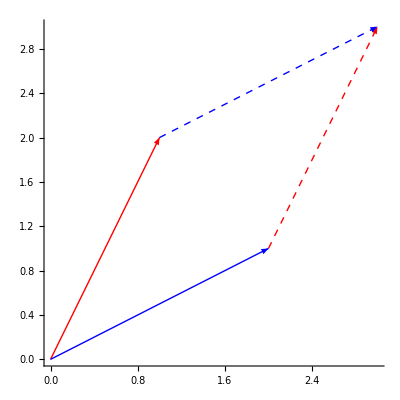

```mathematica
u={1,2};v={2,1};
Graphics[{Red,Arrow[{{0,0},u}],Blue,Arrow[{{0,0},v}],Red,Dashed,Arrow[{v,v+u}],Blue,Dashed,Arrow[{u,u+v}]},Axes->True]
```

## Assignment

Copy and past all problems below into a blank notebook. Include a title, your name, and date at the top of the notebook. Furthermore, be sure to clearly label and evaluate your solutions in such a way that when printed it is easy to grade your work.

Form an augmented matrix to represent the following system. Use RowRedue to determine if the system is consistent and, if so, report the general solution vector.

x_1                               -2 x_4=-3
                2 x_2+2 x_3            =0
                                x_3+3 x_4=1
-2 x_1+3 x_2+2 x_3+   x_4=5

Manually perform the row operations and back-substitution necessary to solve the system corresponding to the following augmented matrix.

```mathematica
aug = {{1,0,3,0,2},{0,1,0,-3,3},{0,-2,3,2,1},{3,0,0,7,-5}}
```

{{1,0,3,0,2},{0,1,0,-3,3},{0,-2,3,2,1},{3,0,0,7,-5}}

Use RowReduce to solve the system below and represent the infinite set of solutions using Graphics3D and Animate.

```mathematica
aug={{1,2,1,3},{-2,-4,-2,-6},{3,6,3,9}};
```

Use Graphics3D to display the linear combination of the following vectors that results in the vector y={8,-7,2}. Additionally, display the commutativity of the aforementioned linear combination.

```mathematica
u1={1,1,1};u2={-2,1,1};u3={1,-2,1};
```